```mathematica
Clear["Global`*"]
SetDirectory["/imports/junko.work/brechtel/Early Warning Signs/Sorted Models/Saddle Node/export"];
```

```mathematica
NormalizeMatrixRows[M_]:=Module[{A=M},
For[i=1,i≤Length[M],++i,
A[[i]]=Normalize[M[[i]],Total]
];
Return[A];
]
```

## Model functions

```mathematica
(*Define functions*)
dx[x_,y_]:=r x(1-x/Kx)-y f[x]
dy[x_,y_]:=y(e f[x]-c -w y)
f[x_]:=a x/(1+a h x)

dispersal[i_,k_]:=-d[[i]]Sum[L[[k,l]]x[i,l][t],{l,Nvertices}]
```

## Parameterization

```mathematica
LoadParameters[]:=Module[{},
S=2;
(* Spatial web *)
Nvertices=6;
L={{3,-1,-1,0,0,-1},{-1,3,-1,0,-1,0},{-1,-1,2,0,0,0},{0,0,0,1,0,-1},{0,-1,0,0,1,0},{-1,0,0,-1,0,2}};

(* parameters *)
r=2;
Kx=10;

e=1;
c=1;
w=0.2;

a=3;
h=0.5;

X0=1;
Y0=1;

d={1,1};
];
```

```mathematica
LoadParameters[];
```

```mathematica
(* Bifurcations *)
(*
	Hopf: a = 2.3 - 2.4
Sattelknoten: Kx=15
*)
```

## Model Equations

```mathematica
(* Homogeneous system equations right hand side *)
rhs[1,k_]:=dx[x[1,k][t],x[2,k][t]]
rhs[2,k_]:=dy[x[1,k][t],x[2,k][t]]
```

```mathematica
Flatten[Table[
x[i,k]'[t]==rhs[i,k],
{i,S},{k,1}]]
```

{x[1,1]'[t]==2 (1-1/10 x[1,1][t]) x[1,1][t]-(3 x[1,1][t] x[2,1][t])/(1+1.5 x[1,1][t]),x[2,1]'[t]==(-1+(3 x[1,1][t])/(1+1.5 x[1,1][t])-0.2 x[2,1][t]) x[2,1][t]}

## Bifurcation Diagram

(-11.7292 | -1.96188
0.00514073 | -0.924839)

(1 | 0
0 | 1)

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

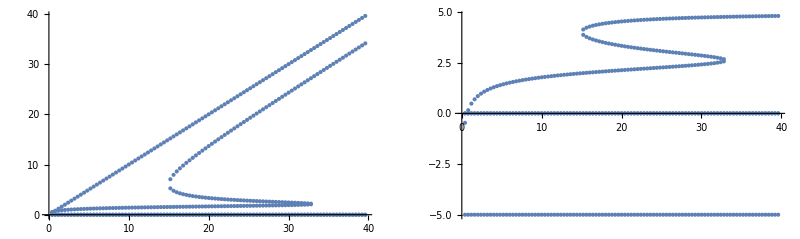

```mathematica
PreyList={};
PredatorList={};
min=0;max=40;
steps=100;
step=(max-min)/steps;
For[i=1,i<steps,++i,
par=min+i*step;
Kx=par;
SteadyStates=Solve[{rhs[1,1]==0,rhs[2,1]==0},{x[1,1][t],x[2,1][t]}];
AppendTo[PreyList,{par,x[1,1][t]}/.SteadyStates];
AppendTo[PredatorList,{par,x[2,1][t]}/.SteadyStates];
];
PreyList=Flatten[PreyList,1];
PredatorList=Flatten[PredatorList,1];
GraphicsRow[{ListPlot[PreyList,PlotRange->All],
ListPlot[PredatorList,PlotRange->All]}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

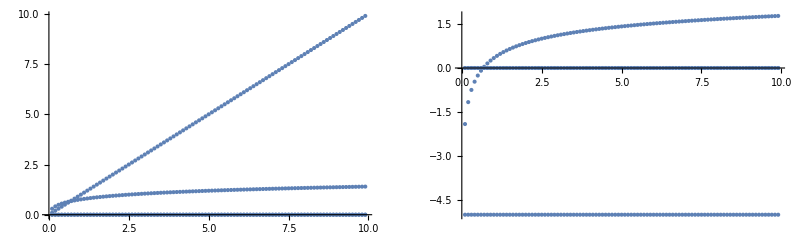

```mathematica
PreyList={};
PredatorList={};
min=0.;max=10.;
steps=100;
step=(max-min)/steps;
For[i=1,i<steps,++i,
par=min+i*step;
Kx=par;
SteadyStates=Solve[{rhs[1,1]==0,rhs[2,1]==0},{x[1,1][t],x[2,1][t]}];
AppendTo[PreyList,{par,x[1,1][t]}/.SteadyStates];
AppendTo[PredatorList,{par,x[2,1][t]}/.SteadyStates];
];
PreyList=Flatten[PreyList,1];
PredatorList=Flatten[PredatorList,1];
GraphicsRow[{ListPlot[PreyList,PlotRange->All],
ListPlot[PredatorList,PlotRange->All]}]
```

```mathematica
Kx=17;
SteadyStates=Solve[{rhs[1,1]==0,rhs[2,1]==0},{x[1,1][t],x[2,1][t]}]//FullSimplify;
TableForm[SteadyStates]

CalculateJacobian[]:=Module[{},
J=D[
Flatten[Table[rhs[i,k],{i,S},{k,1}]],
{Flatten[Table[x[i,k][t],{i,S},{k,1}]]}
];
J0=FullSimplify[J/.SteadyStates[[5]]];
JM=DiagonalMatrix[Table[d[[i]],{i,S}]];
];

CalculateJacobian[];
kappaList=N[Eigenvalues[L]];
J0//MatrixForm
JM//MatrixForm
Eigenvalues[J0]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

x[1,1][t]→0. | x[2,1][t]→-5.
x[1,1][t]→0. | x[2,1][t]→0.
x[1,1][t]→1.58965 | x[2,1][t]→2.04533
x[1,1][t]→4.01521 | x[2,1][t]→3.57607
x[1,1][t]→10.0618 | x[2,1][t]→4.3786
x[1,1][t]→17. | x[2,1][t]→0.

(-0.418207 | -1.87572
0.0507222 | -0.87572)

(1 | 0
0 | 1)

{-0.646963+0.206908 ⅈ,-0.646963-0.206908 ⅈ}

```mathematica
LoadParameters[]
Kx=16
SteadyStates=Solve[{rhs[1,1]==0,rhs[2,1]==0},{x[1,1][t],x[2,1][t]}]//FullSimplify;
RealSteadyStates=Select[SteadyStates,Element[#[[1,2]],Reals]&&Element[#[[2,2]],Reals]&]
TableForm[SteadyStates]
TableForm[RealSteadyStates]

CalculateJacobian[]:=Module[{},
J=D[
Flatten[Table[rhs[i,k],{i,S},{k,1}]],
{Flatten[Table[x[i,k][t],{i,S},{k,1}]]}
];
J0=FullSimplify[J/.SteadyStates[[5]]];
JM=DiagonalMatrix[Table[d[[i]],{i,S}]];
];

CalculateJacobian[];
kappaList=N[Eigenvalues[L]];
J0//MatrixForm
JM//MatrixForm
Eigenvalues[J0]
```

16

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x[1,1][t]→0.,x[2,1][t]→-5.},{x[1,1][t]→0.,x[2,1][t]→0.},{x[1,1][t]→1.56619,x[2,1][t]→2.01429},{x[1,1][t]→4.47362,x[2,1][t]→3.70305},{x[1,1][t]→8.62686,x[2,1][t]→4.28265},{x[1,1][t]→16.,x[2,1][t]→0.}}

x[1,1][t]→0. | x[2,1][t]→-5.
x[1,1][t]→0. | x[2,1][t]→0.
x[1,1][t]→1.56619 | x[2,1][t]→2.01429
x[1,1][t]→4.47362 | x[2,1][t]→3.70305
x[1,1][t]→8.62686 | x[2,1][t]→4.28265
x[1,1][t]→16. | x[2,1][t]→0.

x[1,1][t]→0. | x[2,1][t]→-5.
x[1,1][t]→0. | x[2,1][t]→0.
x[1,1][t]→1.56619 | x[2,1][t]→2.01429
x[1,1][t]→4.47362 | x[2,1][t]→3.70305
x[1,1][t]→8.62686 | x[2,1][t]→4.28265
x[1,1][t]→16. | x[2,1][t]→0.

(-0.222828 | -1.85653
0.0661136 | -0.856531)

(1 | 0
0 | 1)

{-0.53968+0.14949 ⅈ,-0.53968-0.14949 ⅈ}

```mathematica
SteadyStates[[1,1,2]]
```

0.

```mathematica
CalcMaxEigenvalue[]:=Module[{},
Quiet[SteadyStates=Solve[{rhs[1,1]==0,rhs[2,1]==0},{x[1,1][t],x[2,1][t]}]//FullSimplify,Solve::ratnz];
RealSteadyStates=Select[SteadyStates,Element[#[[1,2]],Reals]&&Element[#[[2,2]],Reals]&];

J=D[
Flatten[Table[rhs[i,k],{i,S},{k,1}]],
{Flatten[Table[x[i,k][t],{i,S},{k,1}]]}
];

J0=FullSimplify[J/.RealSteadyStates[[3]]];
JM=DiagonalMatrix[Table[d[[i]],{i,S}]];

kappaList=N[Eigenvalues[L]];

Return[Max[Re[Eigenvalues[J0]]]];
];
```

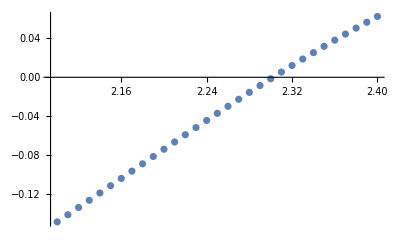

```mathematica
list={};
LoadParameters[];
For[a=2.1,a≤2.4,a+=0.01,
AppendTo[list,{a,CalcMaxEigenvalue[]}];
];
ListPlot[list]
```

```mathematica
Export["H1-Eigenvalues.CSV",list]
```

H1-Eigenvalues.CSV

```mathematica
CalcAllEigenvalues[]:=Module[{},
Quiet[SteadyStates=Solve[{rhs[1,1]==0,rhs[2,1]==0},{x[1,1][t],x[2,1][t]}]//FullSimplify,Solve::ratnz];
RealSteadyStates=Select[SteadyStates,Element[#[[1,2]],Reals]&&Element[#[[2,2]],Reals]&];

J=D[
Flatten[Table[rhs[i,k],{i,S},{k,1}]],
{Flatten[Table[x[i,k][t],{i,S},{k,1}]]}
];

J0=FullSimplify[J/.RealSteadyStates[[3]]];
JM=DiagonalMatrix[Table[d[[i]],{i,S}]];

kappaList=N[Eigenvalues[L]];

Return[Re[Table[Eigenvalues[J0-kappa JM],{kappa,kappaList}]]];
];
```

```mathematica
list={};
LoadParameters[];
For[a=2.1,a≤2.4,a+=0.01,
AppendTo[list,Flatten[{a,CalcAllEigenvalues[]}]];
];
list[[1]]
```

{2.1,-4.54141,-4.54141,-3.8464,-3.8464,-2.50813,-2.50813,-1.28559,-1.28559,-0.561749,-0.561749,-0.148655,-0.148655}

```mathematica
Export["H1-Eigenvalues-all.CSV",list]
```

H1-Eigenvalues-all.CSV

```mathematica
CalcMaxEigenvalue[]:=Module[{},
Quiet[SteadyStates=Solve[{rhs[1,1]==0,rhs[2,1]==0},{x[1,1][t],x[2,1][t]}]//FullSimplify,Solve::ratnz];

J=D[
Flatten[Table[rhs[i,k],{i,S},{k,1}]],
{Flatten[Table[x[i,k][t],{i,S},{k,1}]]}
];

J0=FullSimplify[J/.SteadyStates[[5]]];
JM=DiagonalMatrix[Table[d[[i]],{i,S}]];

kappaList=N[Eigenvalues[L]];

Return[Max[Re[Eigenvalues[J0]]]];
];
```

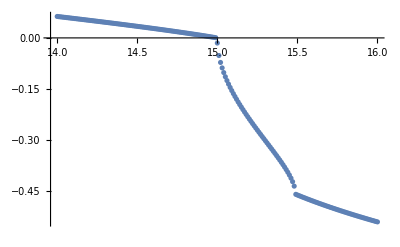

```mathematica
list={};
LoadParameters[];
For[Kx=14,Kx≤16,Kx+=0.01,
AppendTo[list,{Kx,CalcMaxEigenvalue[]}];
];
ListPlot[list]
```

```mathematica
Export["SN1-Eigenvalues.CSV",list]
```

SN1-Eigenvalues.CSV

```mathematica
CalcAllEigenvalue[]:=Module[{},
Quiet[SteadyStates=Solve[{rhs[1,1]==0,rhs[2,1]==0},{x[1,1][t],x[2,1][t]}]//FullSimplify,Solve::ratnz];

J=D[
Flatten[Table[rhs[i,k],{i,S},{k,1}]],
{Flatten[Table[x[i,k][t],{i,S},{k,1}]]}
];

J0=FullSimplify[J/.SteadyStates[[5]]];
JM=DiagonalMatrix[Table[d[[i]],{i,S}]];

kappaList=N[Eigenvalues[L]];

Return[Re[Table[Eigenvalues[J0-kappa JM],{kappa,kappaList}]]];
];
```

```mathematica
list={};
LoadParameters[];
For[Kx=14,Kx≤16,Kx+=0.01,
AppendTo[list,Flatten[{Kx,CalcAllEigenvalues[]}]];
];
list[[1]]
```

{14,-4.07639,-4.07639,-3.38138,-3.38138,-2.04311,-2.04311,-0.82057,-0.82057,-0.0967313,-0.0967313,0.316363,0.316363}

```mathematica
Export["SN1-Eigenvalues-all.CSV",list]
```

SN1-Eigenvalues-all.CSV

```mathematica
list[[100]]
```

{14.99,-4.06742,-4.06742,-3.37241,-3.37241,-2.03413,-2.03413,-0.811595,-0.811595,-0.0877557,-0.0877557,0.325338,0.325338}

## Homogen System

```mathematica
(*set starting conditions*)
setStartHomogen[]:=Module[{delta=0.01},
startHomogen=
Flatten[
Table[
{x[1,k][0]==X0,
x[2,k][0]==Y0},
{k,1}]
];
];

(*Solve ODE*)
solveHomogen[Tmax_]:=Module[{sol},
setStartHomogen[];
sol=NDSolve[Join[{eqnsHomogen,startHomogen}],varsHomogen,{t,0,Tmax},MaxSteps->100000][[1]];
Return[varsHomogen/.sol];
];

EvaluateHomogenSystem[Tmax_]:=Module[{},
(*generate equations*)
eqnsHomogen=Flatten[Table[
x[i,k]'[t]==rhs[i,k],
{i,S},{k,1}]];

(*dependent variables*)
varsHomogen = Flatten[
Table[
x[i,k][t]
,{i,S},{k,1}]
];

(*solve deqns*)
solHomogen=solveHomogen[Tmax];
XSList=solHomogen/.t->Tmax;

(*set steady state values*)
For[i=1,i≤S,++i,
XS[i]=XSList[[i]];
(*TS[i]=Sum[c[[i,j]]XS[j],{j,S}];*)
];
];
```

## Solver

### Local

```mathematica
(* Euler-Verfahren *)
(* ohne Noise *)
EulerLocal[]:=Module[{y},
Tmax=100.;
maxsteps=100000;
dt=Tmax/maxsteps;

data=Table[0,{maxsteps},{i,S}];
eqns=Flatten[Table[rhs[i,k],{i,S},{k,1}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,1}]];

data[[1,1]]=X0;
data[[1,2]]=Y0;

For[step=1,step<maxsteps,step++,
k=1;
For[i=1,i≤S,++i,
y[i,k]=data[[step,i]];
];
data[[step+1]]=data[[step]]+eqns dt;
];
];
```

```mathematica
(* Euler-Maruyama-Verfahren *)
(* Wiener Prozess *)
EulerMaruyamaLocal[noise_,tmax_,maxSteps_]:=Module[{y},
Tmax=tmax;
maxsteps=maxSteps;
dt=Tmax/maxsteps;
Noise[]:=Table[RandomVariate[NormalDistribution[0,Sqrt[dt]]],{S}];
data=Table[0,{maxsteps},{i,S}];
eqns=Flatten[Table[rhs[i,k],{i,S},{k,1}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,1}]];

data[[1,1]]=X0;
data[[1,2]]=Y0;

For[step=1,step<maxsteps,step++,
k=1;
For[i=1,i≤S,++i,
y[i,k]=data[[step,i]];
];
data[[step+1]]=data[[step]]+eqns dt+noise Sqrt[data[[step]]]Noise[];
];
];

EulerMaruyamaLocal[noise_]:=Module[{y},
EulerMaruyamaLocal[noise,100,100000];
];
```

### Spatial

```mathematica
(* Euler-Verfahren *)
(* ohne Noise *)
EulerSpatial[Tmax_,maxsteps_]:=Module[{y},
dt=Tmax/maxsteps;

data=Table[0,{maxsteps},{i,S},{k,Nvertices}];
eqns=FullSimplify[Table[rhs[i,k]+dispersal[i,k],{i,S},{k,Nvertices}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,Nvertices}]];

For[k=1,k≤Nvertices,++k,
data[[1,1,k]]=X0;
data[[1,2,k]]=Y0;
];

For[step=1,step<maxsteps,step++,
For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
y[i,k]=data[[step,i,k]];
];
];
data[[step+1]]=data[[step]]+eqns dt;
];
];
```

```mathematica
(* Euler-Maruyama-Verfahren *)
(* Wiener Prozess *)
EulerMaruyamaSpatial[noise_,Tmax_,maxsteps_]:=Module[{y},
dt=Tmax/maxsteps;

(*noise=0.01;*)
Noise[]:=Table[RandomVariate[NormalDistribution[0,Sqrt[dt]]],{S},{Nvertices}];

data=Table[0,{maxsteps},{i,S},{k,Nvertices}];
eqns=FullSimplify[Table[rhs[i,k]+dispersal[i,k],{i,S},{k,Nvertices}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,Nvertices}]];

For[k=1,k≤Nvertices,++k,
data[[1,1,k]]=X0;
data[[1,2,k]]=Y0;
];

For[step=1,step<maxsteps,step++,
For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
y[i,k]=data[[step,i,k]];
];
];
data[[step+1]]=data[[step]]+eqns dt+noise Sqrt[data[[step]]]Noise[];
];
];
```

```mathematica
EulerMaruyamaSpatial[noise_,Tmax_,maxsteps_,initialData_]:=Module[{y},
dt=Tmax/maxsteps;

(*noise=0.01;*)
Noise[]:=Table[RandomVariate[NormalDistribution[0,Sqrt[dt]]],{S},{Nvertices}];

data=Table[0,{maxsteps},{i,S},{k,Nvertices}];
eqns=FullSimplify[Table[rhs[i,k]+dispersal[i,k],{i,S},{k,Nvertices}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,Nvertices}]];

data[[1]]=initialData;

For[step=1,step<maxsteps,step++,
For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
y[i,k]=data[[step,i,k]];
];
];
data[[step+1]]=data[[step]]+eqns dt+noise Sqrt[data[[step]]]Noise[];
];
];
```

### Local variable Kx

```mathematica
(* Euler-Verfahren *)
(* ohne Noise *)
EulerLocalVariable[KxInterval_]:=Module[{y,Kxstep,Kxt,step},
Tmax=100.;
maxsteps=100000;
dt=Tmax/maxsteps;

Kxstep=(KxInterval[[2]]-KxInterval[[1]])/maxsteps;
Kx=Kxt;

data=Table[0,{maxsteps},{i,S}];
eqns=Flatten[Table[rhs[i,k],{i,S},{k,1}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,1}]];

data[[1,1]]=X0;
data[[1,2]]=Y0;

For[step=1,step<maxsteps,step++,
Kxt=KxInterval[[1]]+step Kxstep;
k=1;
For[i=1,i≤S,++i,
y[i,k]=data[[step,i]];
];
data[[step+1]]=data[[step]]+eqns dt;
];
];
```

```mathematica
(* Euler-Maruyama-Verfahren *)
(* Wiener Prozess *)
EulerMaruyamaLocalVariable[KxInterval_,noise_,tmax_,maxSteps_]:=Module[{y,Kxstep,Kxt,step},
Tmax=tmax;
maxsteps=maxSteps;
dt=Tmax/maxsteps;

Kxstep=(KxInterval[[2]]-KxInterval[[1]])/maxsteps;
Kx=Kxt;

Noise[]:=Table[RandomVariate[NormalDistribution[0,Sqrt[dt]]],{S}];
data=Table[0,{maxsteps},{i,S}];
eqns=Flatten[Table[rhs[i,k],{i,S},{k,1}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,1}]];

data[[1,1]]=X0;
data[[1,2]]=Y0;

For[step=1,step<maxsteps,step++,
Kxt=KxInterval[[1]]+step Kxstep;
k=1;
For[i=1,i≤S,++i,
y[i,k]=data[[step,i]];
];
data[[step+1]]=data[[step]]+eqns dt+noise Sqrt[data[[step]]]Noise[];
];
];

EulerMaruyamaLocalVariable[KxInterval_,noise_]:=Module[{y},
EulerMaruyamaLocalVariable[KxInterval,noise,100,100000];
];
```

### Spatial variable Kx

```mathematica
(* Euler-Verfahren *)
(* ohne Noise *)
EulerSpatialVariable[KxInterval_]:=Module[{y,Kxstep,Kxt,step},
Tmax=500.;
maxsteps=100000;
dt=Tmax/maxsteps;

Kxstep=(KxInterval[[2]]-KxInterval[[1]])/maxsteps;
Kx=Kxt;

data=Table[0,{maxsteps},{i,S},{k,Nvertices}];
eqns=FullSimplify[Table[rhs[i,k]+dispersal[i,k],{i,S},{k,Nvertices}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,Nvertices}]];

For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
data[[1,1,k]]=X0;
data[[1,2,k]]=Y0;
];
];

For[step=1,step<maxsteps,step++,
Kxt=KxInterval[[1]]+step Kxstep;
For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
y[i,k]=data[[step,i,k]];
];
];
data[[step+1]]=data[[step]]+eqns dt;
];
];
```

```mathematica
(* Euler-Maruyama-Verfahren *)
(* Wiener Prozess *)
EulerMaruyamaSpatialVariable[KxInterval_,noise_,tmax_,maxSteps_]:=Module[{y,Kxstep,Kxt},
Tmax=tmax;
maxsteps=maxSteps;
dt=Tmax/maxsteps;

Kxstep=(KxInterval[[2]]-KxInterval[[1]])/maxsteps;
Kx=Kxt;

Noise[]:=Table[RandomVariate[NormalDistribution[0,Sqrt[dt]]],{S},{Nvertices}];

data=Table[0,{maxsteps},{i,S},{k,Nvertices}];
eqns=FullSimplify[Table[rhs[i,k]+dispersal[i,k],{i,S},{k,Nvertices}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,Nvertices}]];

For[k=1,k≤Nvertices,++k,
data[[1,1,k]]=X0;
data[[1,2,k]]=Y0;
];

For[step=1,step<maxsteps,step++,
Kxt=KxInterval[[1]]+step Kxstep;
For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
y[i,k]=data[[step,i,k]];
];
];
data[[step+1]]=data[[step]]+eqns dt+noise Sqrt[data[[step]]]Noise[];
];
];

EulerMaruyamaSpatialVariable[KxInterval_,noise_]:=Module[{y},
EulerMaruyamaSpatialVariable[KxInterval,noise,100,100000];
];

EulerMaruyamaSpatialVariable[KxInterval_,noise_,tmax_,maxSteps_,initialData_]:=Module[{y,Kxt,Kxstep},
Tmax=tmax;
maxsteps=maxSteps;
dt=Tmax/maxsteps;

Kxstep=(KxInterval[[2]]-KxInterval[[1]])/maxsteps;
Kx=Kxt;

Noise[]:=Table[RandomVariate[NormalDistribution[0,Sqrt[dt]]],{S},{Nvertices}];

data=Table[0,{maxsteps},{i,S},{k,Nvertices}];
eqns=FullSimplify[Table[rhs[i,k]+dispersal[i,k],{i,S},{k,Nvertices}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,Nvertices}]];

data[[1]]=initialData;

For[step=1,step<maxsteps,step++,
Kxt=KxInterval[[1]]+step Kxstep;
For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
y[i,k]=data[[step,i,k]];
];
];
data[[step+1]]=data[[step]]+eqns dt+noise Sqrt[data[[step]]]Noise[];
];
];
```

### Spatial variable a

```mathematica
(* Euler-Verfahren *)
(* ohne Noise *)
EulerSpatialVariableA[aInterval_]:=Module[{y,astep,at,step},
Tmax=500.;
maxsteps=100000;
dt=Tmax/maxsteps;

astep=(aInterval[[2]]-aInterval[[1]])/maxsteps;
a=at;

data=Table[0,{maxsteps},{i,S},{k,Nvertices}];
eqns=FullSimplify[Table[rhs[i,k]+dispersal[i,k],{i,S},{k,Nvertices}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,Nvertices}]];

For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
data[[1,1,k]]=X0;
data[[1,2,k]]=Y0;
];
];

For[step=1,step<maxsteps,step++,
at=aInterval[[1]]+step astep;
For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
y[i,k]=data[[step,i,k]];
];
];
data[[step+1]]=data[[step]]+eqns dt;
];
];
```

```mathematica
(* Euler-Maruyama-Verfahren *)
(* Wiener Prozess *)
EulerMaruyamaSpatialVariableA[aInterval_,noise_,tmax_,maxSteps_]:=Module[{y,astep,at},
Tmax=tmax;
maxsteps=maxSteps;
dt=Tmax/maxsteps;

astep=(aInterval[[2]]-aInterval[[1]])/maxsteps;
a=at;

Noise[]:=Table[RandomVariate[NormalDistribution[0,Sqrt[dt]]],{S},{Nvertices}];

data=Table[0,{maxsteps},{i,S},{k,Nvertices}];
eqns=FullSimplify[Table[rhs[i,k]+dispersal[i,k],{i,S},{k,Nvertices}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,Nvertices}]];

For[k=1,k≤Nvertices,++k,
data[[1,1,k]]=X0;
data[[1,2,k]]=Y0;
];

For[step=1,step<maxsteps,step++,
at=aInterval[[1]]+step astep;
For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
y[i,k]=data[[step,i,k]];
];
];
data[[step+1]]=data[[step]]+eqns dt+noise Sqrt[data[[step]]]Noise[];
];
];

EulerMaruyamaSpatialVariableA[aInterval_,noise_]:=Module[{y},
EulerMaruyamaSpatialVariableA[aInterval,noise,100,100000];
];

EulerMaruyamaSpatialVariableA[aInterval_,noise_,tmax_,maxSteps_,initialData_]:=Module[{y,at,astep},
Tmax=tmax;
maxsteps=maxSteps;
dt=Tmax/maxsteps;

astep=(aInterval[[2]]-aInterval[[1]])/maxsteps;
a=at;

Noise[]:=Table[RandomVariate[NormalDistribution[0,Sqrt[dt]]],{S},{Nvertices}];

data=Table[0,{maxsteps},{i,S},{k,Nvertices}];
eqns=FullSimplify[Table[rhs[i,k]+dispersal[i,k],{i,S},{k,Nvertices}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,Nvertices}]];

data[[1]]=initialData;

For[step=1,step<maxsteps,step++,
at=aInterval[[1]]+step astep;
For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
y[i,k]=data[[step,i,k]];
];
];
data[[step+1]]=data[[step]]+eqns dt+noise Sqrt[data[[step]]]Noise[];
];
];
```